# h-BN

First, consider the valence electron configurations:

Boron (B) → 1s.b2 2s.b2 2p.b9 → 3 valence electrons

Nitrogen (N) → 1s.b2 2s.b2 2p.b3 → 5 valence electrons

So together, B–N pair has: 
3+5=8 valence electrons

. But in the crystal, the picture becomes 2D and delocalized, which means the quantum wavefunction extend over many atoms rather that being on a single atom. This spreading out lowers the system’s energy.

Boron has only 3 valence electrons → it makes 3 σ-bonds via sp.b2 hybrids.
→ No electrons left for π directly.
→ Its pᶻ orbital stays empty in the band picture (but exists for bonding).

Nitrogen has 5 valence electrons → it makes 3 σ-bonds via sp.b2 hybrids.
→ 2 electrons left → lone pair or π electrons.
→ Its pᶻ orbital is partly occupied, forming the top of the π-band.
-------------------------------------
ABOUT LONE PAIR OR PI DELOCALIZED

the consensus is:

N’s two leftover electrons mainly stay as a lone pair in an sp.b2 orbital.

The π-band comes from N’s remaining pᶻ electrons, but B’s empty pᶻ orbital pulls some electron density, creating partial ionic character.

How verified?

DFT calculations → show electron density mostly on N in the π-band.

X-ray photoelectron spectroscopy (XPS) → confirms different electron densities on B vs. N.

Band structure experiments (ARPES) → match the calculated π-band shape and gap.

So while subtle, it’s experimentally confirmed that N keeps a lone pair and also fills the π-band more than B.
-------------------------------------
About Bonding

Covalent character: electrons are shared in σ-bonds → strong mechanical stability.

Ionic character: electrons in the π-system favor N → opens the large band gap → makes h-BN an insulator.

This mixed covalent-ionic bonding is why h-BN is:

-Chemically very stable

-Electrically insulating

-Structurally very strong (like graphene)

----------------------------------------

In monolayer h-BN (or graphene):

Each atom has a pᶻ orbital sticking up or down out of the plane.

These orbitals overlap sideways with neighboring pᶻ orbitals.

Electrons in these orbitals aren’t trapped between just two atoms but instead form Bloch waves extending across the entire crystal.

So rather than belonging to a single B–N bond, a π electron has a probability of being found anywhere in the sheet.

Delocalization:

✅ Lowers the energy (electrons spread out → more stability)
✅ Allows electrical conduction (in conductors like graphene)
✅ Creates bands in the electronic structure

In h-BN, although the π electrons are delocalized, the on-site energy difference between B and N means the electrons still “prefer” the N atoms. That’s why the material remains an insulator despite having delocalized bands.

Just like carbon in graphene, both B and N hybridize their orbitals

Each atom mixes its 2s, 2pₓ, 2pᵧ orbitals → makes three sp.b2 hybrids.

These sp.b2 hybrids form σ-bonds in-plane:


We are starting with the simplest way of plotting the h-BN band structure, using tight binding.

Recall: Tight Binding assumes the wavefunction of the system can be expanded as atomic orbitals. 

As in graphene, we keep just the out-of-plane pz orbital per atom and form Bloch sums.

The difference with Graphene (two equal orbitals in each unit cell) is there are now two inequivalent orbitals in each unit cell, one on Boron and one on N, and different onsite energies.

```mathematica
Quit
```

```mathematica
(*1. Lattice vectors---*)
a=2.50; 

(*lattice constant,set to 1 for simplicity*)
a1={3/2,-Sqrt[3]/2}*a;
a2={3/2,Sqrt[3]/2}*a;
```

```mathematica
(*2. Parameters*)
t=2.9;                            (*eV*)
Δ=5.8;
```

```mathematica
(*here is important the coordinate system
  N
  \
 delta 2
     \   
      B - delta1 - N
     /
delta 3  
  / 
 N
      
*)
```

```mathematica
delta1=(a1+a2)/3;
```

```mathematica
delta2=(-2*a1/3+a2/3);
```

```mathematica
delta3=(a1/3-2*a2/3);
```

```mathematica
deltas={delta1,delta2,delta3};
```

```mathematica
(*---Gamma(k) function---*)
gamma[kx_,ky_]:=N[Total[Exp[I*(kx*#[[1]]+ky*#[[2]])]&/@deltas]];
```

```mathematica
(*For each δ=(δₓ,δᵧ),it computes exp(i*(kx*δₓ+ky*δᵧ)).*)
```

```mathematica
H[kx_,ky_]:={{Δ/2,t*gamma[kx,ky]},{t*Conjugate[gamma[kx,ky]],-Δ/2}};
```

```mathematica
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]]
(*Test at Γ*)
```

```mathematica
eigenvals[0.,0.]
```

{-9.17061,9.17061}

```mathematica
(*--Define the path--*)
```

```mathematica
(*Compute reciprocal lattice vectors*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};
```

```mathematica
kΓ={0,0};
kK=(1/3)*(b1-b2);
kM=(1/2)*b1;
```

```mathematica
kPath=Join[Table[(1-s) kΓ+s kK,{s,0,1,0.01}],Table[(1-s) kK+s kM,{s,0,1,0.01}],Table[(1-s) kM+s kΓ,{s,0,1,0.01}]];
```

```mathematica
kDistances=
Prepend[
Accumulate[
Norm/@Differences[kPath]
],
0
];
```

```mathematica
bands=eigenvals@@@kPath;
bandsPlus=bands[[All,2]];
bandsMinus=bands[[All,1]];
```

```mathematica
symmetryPoints={1,Length[kPath]/3,2*Length[kPath]/3,Length[kPath]};
tickPositions=kDistances[[Round[symmetryPoints]]];
tickLabels={"Γ","K","M","Γ"};
ticks=Transpose[{tickPositions,tickLabels}];
```

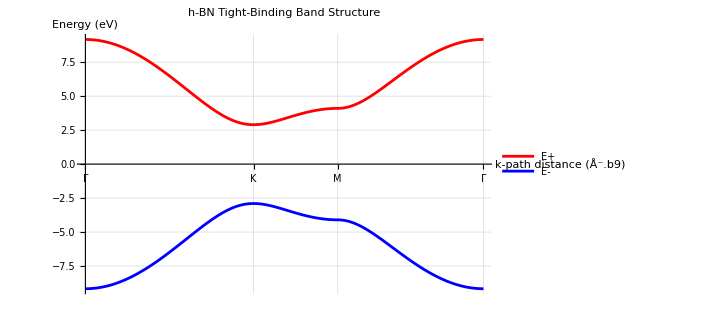

```mathematica
(*Build explicit {x,y} pairs*)
bandsPlusData=Transpose[{kDistances,bandsPlus}];
bandsMinusData=Transpose[{kDistances,bandsMinus}];

(*Plot each band separately and overlay them*)
Show[ListLinePlot[bandsPlusData,Joined->True,PlotStyle->Red,PlotLegends->{"E+"}],ListLinePlot[bandsMinusData,Joined->True,PlotStyle->Blue,PlotLegends->{"E-"}],Ticks->{{{kDistances[[1]],"Γ"},{kDistances[[Length[kPath]/3]],"K"},{kDistances[[2*Length[kPath]/3]],"M"},{kDistances[[Length[kPath]]],"Γ"}},Automatic},AxesLabel->{"k-path distance (Å⁻.b9)","Energy (eV)"},GridLines->Automatic,PlotLabel->"h-BN Tight-Binding Band Structure",PlotRange->All]
```